```mathematica
Gett2[totrates_]:=Module[{slist,ltotr,R,u,dt},
slist=Insert[Accumulate[totrates],0,1];
ltotr=Length[totrates];(*Length[totrates];*)
R= slist[[-1]];(*Total[totrates];*)
u=RandomReal[{0,1}];
dt = (1/R )*Log[1/u];
dt
];

vars={{1},{2,4},5,100};(*{Ds,Phis,m,tmax}*)
tpar={0.1,0.001,0.001,0.1,0.1,0.1,0.1,0.1};(* JhR,JlL->0 for hole and electron blocking at anode and cathode *)
{kappa,gamma}={0.005,0.005};
BlockInjection={False,True};(*{True,True};*)
Er=0.8;(*10^6*ev/cm * 5nm*)
w0=1;beta=40;(*beta=40 for Temp=0.025; for 300K*)
M=5;wv=0.2;lam=1; (* vibrational assistance for HOMO-LUMO hops*)

AlwaysLP=True;
```

```mathematica
ntraj=1;
maxiter=30;
current={};
gs=Range[1,5,5];(*{0.05,0.1,0.5,1,2}*);
res={};alloutt={};
Do[
Print["================= gg = ",gg,"================="];
alloutx={};
Do[
If[Mod[itraj,5]==0,Print[" traj = ",itraj]];
out=trajectory[8,vars,gg,tpar,kappa,gamma,Er,w0,beta,maxiter,True,BlockInjection,M,wv,lam,AlwaysLP];
Print["ZQ: ",Sort[out[[1,All,-1]]//Tally]];
AppendTo[alloutx,out];
,{itraj,1,ntraj}];
AppendTo[alloutt,alloutx];
,{gg,gs}];
```

================= gg = 1=================

Eigensystem::arh: Because finding 127 out of the 127 eigenvalues and/or eigenvectors is likely to be faster with dense matrix methods, the sparse input matrix will be converted. If fewer eigenvalues and/or eigenvectors would be sufficient, consider restricting this number using the second argument to Eigensystem.

Eigensystem::arh: Because finding 120 out of the 120 eigenvalues and/or eigenvectors is likely to be faster with dense matrix methods, the sparse input matrix will be converted. If fewer eigenvalues and/or eigenvectors would be sufficient, consider restricting this number using the second argument to Eigensystem.

Eigensystem::arh: Because finding 128 out of the 128 eigenvalues and/or eigenvectors is likely to be faster with dense matrix methods, the sparse input matrix will be converted. If fewer eigenvalues and/or eigenvectors would be sufficient, consider restricting this number using the second argument to Eigensystem.

General::stop: Further output of Eigensystem::arh will be suppressed during this calculation.

$Aborted

pf for ZT: {0.000167731,2.69009×10^-32}{1.94232×10^-20,0.305071}

N = {3,2,4,2,2,2,4,2,2,2,4,5,3,4,2,3,3,3,4,3,2,4,4,4,4,2,4,4,3,3}

m = {5,4,5,5,5,6,7,6,7,8,9,10,9,9,9,10,11,12,12,11,11,12,12,13,14,14,15,16,15,16}

j = {{4,11},{8,6},{5,5},{20,3},{16,2},{9,2},{21,1}}

ZQ: {{0,17},{1,13}}

```mathematica
out[[1,All,-3;;-1].]
```

Part::partd: Part specification out⟦1,All,-3;;-1⟧ is longer than depth of object.

out⟦1,All,-3;;-1⟧

```mathematica
out[[1,All,7;;8]]
```

{{3,5},{2,4},{4,5},{2,5},{2,5},{2,6},{4,7},{2,6},{2,7},{2,8},{4,9},{5,10},{3,9},{4,9},{2,9},{3,10},{3,11},{3,12},{4,12},{3,11},{2,11},{4,12},{4,12},{4,13},{4,14},{2,14},{4,15},{4,16},{3,15},{3,16}}

```mathematica
current={};
nav=5;
ig=0;
Is={};Ivsg={};Ivsg2={};Ivsg2s={};
charg={};tms={};rc={};times12={};Ivsg3={}
Do[
ig+=1;
alloutx=alloutt[[ig]];
Ix={};chargx={};Ix2={};Ix3={};
tm=0;rcx={};
Do[

{out2,Evst}=alloutx[[itraj]];
charges=out2[[All,3]];
tottime=out2[[-1,2]];
AppendTo[Ix,Total[charges]/tottime];

rates=out2[[All,10]];
tottime2=0;
xx=rates[[All,9;;24]];

AppendTo[Ix3,Total[charges]/Total[Gett2/@rates]];

(*Print[" -----  g= ",gg];
Sort[charges//Tally]//Print;*)

Do[
dts=Gett2/@xx;
tottime2+=Total[dts];
,{ii,1,nav}];
tottime2=tottime2/nav;

(*If[itraj==1,times12x =Gettpm/@xx];
times12x +=Gettpm/@xx;
*)
AppendTo[rcx,Total[Total[xx]]];

AppendTo[Ix2,Total[charges]/tottime2];
AppendTo[chargx,Total[charges]];

tm +=tottime2;
,{itraj,1,ntraj}];

tm=tm/ntraj;

(*AppendTo[times12,times12x/ntraj];*)
AppendTo[rc,{gg,Total[rcx]}];
AppendTo[tms,{gg,tm}];
AppendTo[Is,Ix];
AppendTo[Ivsg,{gg,Total[Ix]}];
AppendTo[Ivsg2,{gg,Total[Ix2]}];
AppendTo[Ivsg3,{gg,Total[Ix3]}];
AppendTo[Ivsg2s,Ix2];
AppendTo[charg,{gg,Total[chargx]}];
,{gg,gs}];
```

{}

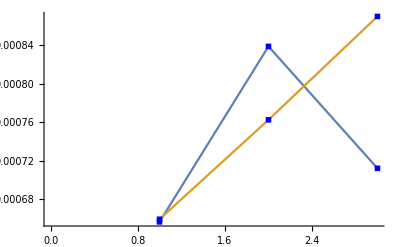

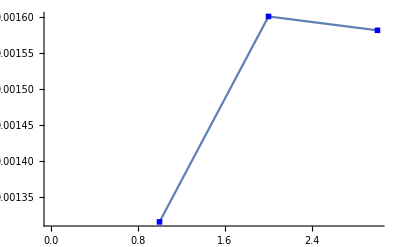

```mathematica
ListPlot[Is//Transpose,Joined->True,PlotMarkers->Style["■", Small, Blue]]
ListPlot[Total[Is//Transpose],Joined->True,PlotMarkers->Style["■", Small, Blue]]
```

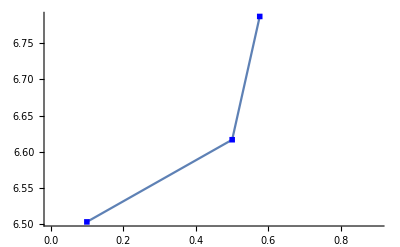

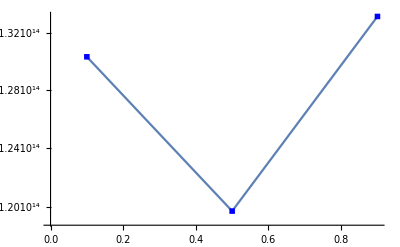

```mathematica
ListPlot[rc,Joined->True,PlotMarkers->Style["■", Small, Blue]]
ListLogPlot[tms,Joined->True,PlotMarkers->Style["■", Small, Blue]]
```

```mathematica
x=Transpose[Ivsg2s];
y=Accumulate[x];
Manipulate[ListPlot[y[[i]]/i,Joined->True,PlotMarkers->{"X"}],{i,1,Length[y],1}]
```

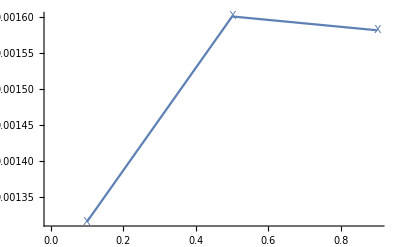

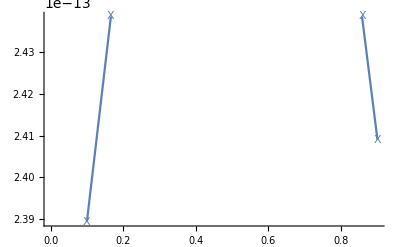

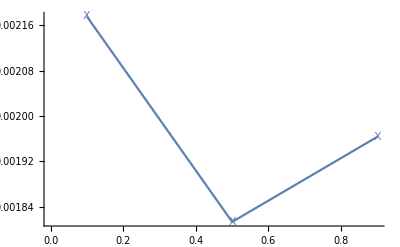

```mathematica
ListPlot[{Ivsg},Joined->True,PlotMarkers->{"X"}]
ListPlot[{Ivsg2},Joined->True,PlotMarkers->{"X"}]
ListPlot[{Ivsg3},Joined->True,PlotMarkers->{"X"}]
```

```mathematica
charg
```

{{0.1,31},{0.5,32},{0.9,32}}